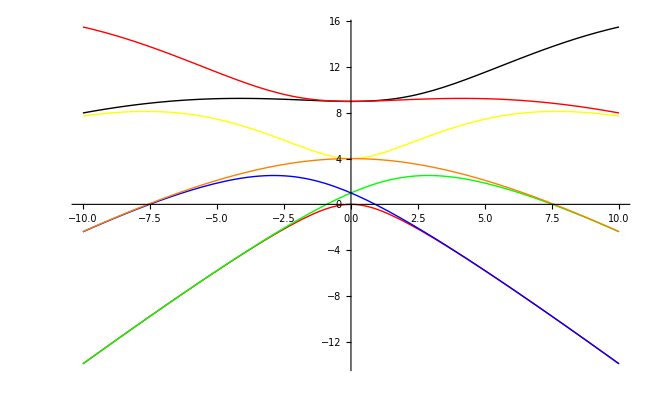

```mathematica
Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicA[1,q],MathieuCharacteristicB[1,q],MathieuCharacteristicA[2,q],MathieuCharacteristicB[2,q],MathieuCharacteristicA[3,q],MathieuCharacteristicB[3,q]},{q,-10,10},PlotStyle->{Red,Green,Blue,Yellow,Orange,Black}]
```

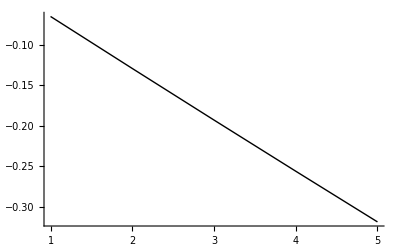

```mathematica
fx[n_,q_]:=(MathieuCharacteristicA[n,q]-MathieuCharacteristicA[0,q])/MathieuCharacteristicA[0,q];
ListPlot[Table[fx[n,1000],{n,1,5}],PlotStyle->{Red,Green,Blue,Yellow,Orange,Black},PlotRange->All,Joined->True]
```

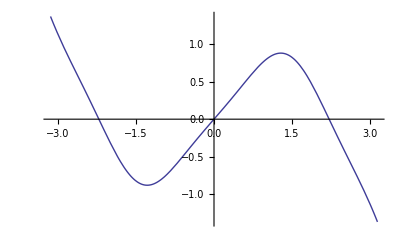

```mathematica
Plot[{Im[MathieuS[1,1,x]]},{x,-π,π}]
```

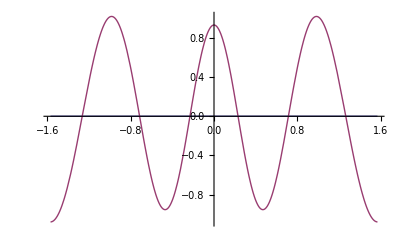

```mathematica
Plot[{0,Re[MathieuC[MathieuCharacteristicA[6,-5],-5,x]]},{x,-π/2,π/2},PlotRange->All]
```

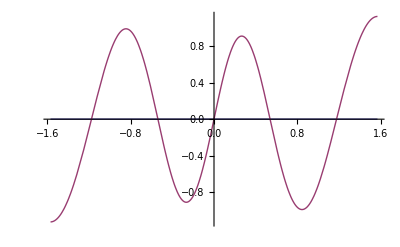

```mathematica
Plot[{0,MathieuS[MathieuCharacteristicB[5,-5],-5,x]},{x,-π/2,π/2},PlotRange->All]
```

```mathematica
N[MathieuS[MathieuCharacteristicB[2,-5],-5,π]]
```

-5.10118×10^-16+6.61744×10^-24 ⅈ

```mathematica
(* Analyzing the coupled oscillator *)
Clear[data,len];
data=Import["POLLT40.dat"];
len=Length[data]
```

10000

```mathematica
Clear[av11,av12,av13,av21,av22,av23,av31,av32,av33];
Clear[er11,er12,er13,er21,er22,er23,er31,er32,er33];
Clear[eval,eval1,eval2];
TMAX=10;
NDAT=10000;
For[t=1,t≤TMAX,t++,
Clear[corr11,corr12,corr13,corr21,corr22,corr23,corr31,corr32,corr33];
corr11=Table[data[[n,2]],{n,t,NDAT,10}];
corr12=Table[data[[n,3]],{n,t,NDAT,10}];
corr13=Table[data[[n,4]],{n,t,NDAT,10}];
corr21=Table[data[[n,5]],{n,t,NDAT,10}];
corr22=Table[data[[n,6]],{n,t,NDAT,10}];
corr23=Table[data[[n,7]],{n,t,NDAT,10}];
corr31=Table[data[[n,8]],{n,t,NDAT,10}];
corr32=Table[data[[n,9]],{n,t,NDAT,10}];
corr33=Table[data[[n,10]],{n,t,NDAT,10}];
avg11[t]=Mean[corr11];
err11[t]=Sqrt[StandardDeviation[corr11]/len];
avg12[t]=Mean[corr12];
err12[t]=Sqrt[StandardDeviation[corr12]/len];
avg13[t]=Mean[corr13];
err13[t]=Sqrt[StandardDeviation[corr13]/len];
avg21[t]=Mean[corr21];
err21[t]=Sqrt[StandardDeviation[corr21]/len];
avg22[t]=Mean[corr22];
err22[t]=Sqrt[StandardDeviation[corr22]/len];
avg23[t]=Mean[corr23];
err23[t]=Sqrt[StandardDeviation[corr23]/len];
avg31[t]=Mean[corr31];
err31[t]=Sqrt[StandardDeviation[corr31]/len];
avg32[t]=Mean[corr32];
err32[t]=Sqrt[StandardDeviation[corr32]/len];
avg33[t]=Mean[corr33];
err33[t]=Sqrt[StandardDeviation[corr33]/len];
]
(* Print the correlation matrix *)
For[t=1,t≤TMAX,t++,
(*Print[t," ",avg11[t]," ",err11[t]];
Print[t," ",avg12[t]," ",err12[t]];
Print[t," ",avg33[t]," ",err33[t]];*)
Clear[mat];
mat={{avg11[t],avg12[t],avg13[t]},{avg21[t],avg22[t],avg23[t]},{avg31[t],avg32[t],avg33[t]}};
(*Print[MatrixForm[mat]];*)
eval=Eigenvalues[mat];
eval1[t]=eval[[1]];
eval2[t]=eval[[2]];
eval3[t]=eval[[3]];
Print[t," ",eval1[t]," ",eval2[t]," ",eval3[t]]
]
```

1 1.31737 0.866284 0.552495

2 1.39728 0.753355 0.355721

3 1.2813 0.68847 0.335792

4 1.22855 0.621993 0.278921

5 1.20004 0.557945 0.216516

6 1.17652 0.498872 0.162228

7 1.03417 0.489196 0.192883

8 1.11317 0.402444 0.092612

9 1.00877 0.39229 0.110658

10 1.03584 0.331651 0.0576735

{0.866284,0.753355,0.68847,0.621993,0.557945,0.498872,0.489196,0.402444,0.39229,0.331651}

{0.552495,0.355721,0.335792,0.278921,0.216516,0.162228,0.192883,0.092612,0.110658,0.0576735}

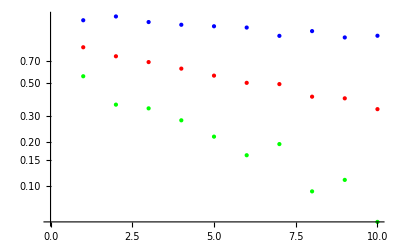

```mathematica
Clear[e1,e2,e3];
e1=Table[eval1[t],{t,1,10}];
e2=Table[eval2[t],{t,1,10}]
e3=Table[eval3[t],{t,1,10}]
ListLogPlot[{e1,e2,e3},PlotStyle->{{PointSize[Large],Blue},{PointSize[Large],Red},{PointSize[Large],Green}}]
```

```mathematica
For[i=1,i<TMAX,i++,
Print[i," ",Log[eval1[i]/eval1[i+1]]," ",Log[eval2[i]/eval2[i+1]]," ",Log[eval3[i]/eval3[i+1]]];
]
```

1 -0.0588924 0.139676 0.440298

2 0.086657 0.0900649 0.0576537

3 0.0420424 0.101542 0.185565

4 0.0234773 0.108669 0.253264

5 0.0197929 0.111911 0.288664

6 0.12896 0.0195877 -0.173082

7 -0.073615 0.195207 0.733663

8 0.0984817 0.0255546 -0.178026

9 -0.0264742 0.167917 0.651648

```mathematica
(BesselI[1,0.01]/BesselI[0,0.01])*(BesselI[-1,0.01]/BesselI[0,0.01])*(BesselI[1,0.02]/BesselI[0,0.02])
```

2.49981×10^-7

```mathematica
(* Analyzing the coupled oscillator: Analysis 2 *)
Clear[data,len];
data=Import["POLLT40.dat"];
len=Length[data]
```

50000

```mathematica
Clear[av11,av22,av33];
Clear[er11,er22,er33];
Clear[eval,eval1,eval2,eval3];
Clear[t,i,TMAX,NDAT];
TMAX=10;
NDAT=len/TMAX;
For[t=1,t≤TMAX,t++,
av11[t]=0.0;av22[t]=0.0;av33[t]=0.0;
er11[t]=0.0;er22[t]=0.0;er33[t]=0.0;
]
For[i=1,i≤NDAT,i++,
For[t=1,t≤TMAX,t++,
Clear[corr11,corr12,corr13,corr21,corr22,corr23,corr31,corr32,corr33];
corr11=data[[(i-1)*TMAX+t,2]];
corr12=data[[(i-1)*TMAX+t,3]];
corr13=data[[(i-1)*TMAX+t,4]];
corr21=data[[(i-1)*TMAX+t,5]];
corr22=data[[(i-1)*TMAX+t,6]];
corr23=data[[(i-1)*TMAX+t,7]];
corr31=data[[(i-1)*TMAX+t,8]];
corr32=data[[(i-1)*TMAX+t,9]];
corr33=data[[(i-1)*TMAX+t,10]];
(* Create and diagonalize the correlation matrix *)
Clear[mat];
mat={{corr11,corr12,corr13},{corr21,corr22,corr23},{corr31,corr32,corr33}};
eval=Eigenvalues[mat];
av11[t]=av11[t]+eval[[1]];
er11[t]=er11[t]+eval[[1]]*eval[[1]];
av22[t]=av22[t]+eval[[2]];
er22[t]=er22[t]+eval[[2]]*eval[[2]];
av33[t]=av33[t]+eval[[3]];
er33[t]=er33[t]+eval[[3]]*eval[[3]];
]
]
For[t=1,t≤TMAX,t++,
av11[t]=av11[t]/NDAT; 
er11[t]=er11[t]/NDAT - av11[t]^2;
If[er11[t]≥0.0,er11[t]=Sqrt[er11[t]/NDAT],Print["Error"]];
av22[t]=av22[t]/NDAT; 
er22[t]=er22[t]/NDAT - av22[t]^2;
If[er22[t]≥0.0,er22[t]=Sqrt[er22[t]/NDAT],Print["Error"]];
av33[t]=av33[t]/NDAT; 
er33[t]=er33[t]/NDAT - av33[t]^2;
If[er33[t]≥0.0,er33[t]=Sqrt[er33[t]/NDAT],Print["Error"]];
]
```

Error

Error

Error

«8 more identical outputs»

```mathematica
Clear[outfile];
outfile=OpenWrite["evals.dat",FormatType->OutputForm];
For[t=1,t≤TMAX,t++,
(*Write[outfile,t," ",av11[t]," ",NumberForm[CForm[er11[t]],4]," ",av22[t]," ",CForm[er22[t]]," ",av33[t]," ",CForm[er33[t]]];*)
no=NumberForm[er11[t],6];
Print[t," ",av11[t]," ",no," ",av22[t]," ",er22[t]," ",av33[t]," ",er33[t]];
]
Close[outfile];
```

1 0.98 3.67125×10^-9 0.92237 5.83433×10^-9 0.83378 5.17051×10^-9

2 0.9604 4.29298×10^-9 0.85077 1.37382×10^-9 0.69519 4.47655×10^-9

3 0.94119 5.27678×10^-9 0.78473 3.4819×10^-9 0.57964 2.08616×10^-9

4 0.92236 2.42573×10^-9 0.72381 4.19621×10^-9 0.48329 2.56478×10^-9

5 0.90392 -1.88738×10^-13 0.66762 -8.2323×10^-14 0.40296 1.97967×10^-9

6 0.88584 5.61123×10^-9 0.6158 -3.54161×10^-14 0.33598 -5.38458×10^-15

7 0.86812 -2.58682×10^-14 0.56799 1.38989×10^-9 0.28014 -1.3739×10^-15

8 0.85076 3.83108×10^-9 0.5239 -2.38698×10^-15 0.23357 -3.00454×10^-15

9 0.83374 -1.20237×10^-13 0.48323 -4.08007×10^-15 0.19475 -2.76862×10^-15

10 0.81706 5.1898×10^-9 0.44572 9.9682×10^-10 0.16238 0.

```mathematica
(* For the free case, when the oscillators are not coupled *)
Clear[data,c1,c2,c3,m1,m2,m3];
data=Import["POLLT40.dat"];
Length[data]
```

10000

```mathematica
For[t=1,t≤10,t++,
Clear[c];
c=Table[data[[n,2]],{n,t,10000,10}];
c1[t]=Mean[c];
Clear[c];
c=Table[data[[n,6]],{n,t,10000,10}];
c2[t]=Mean[c];
Clear[c];
c=Table[data[[n,10]],{n,t,10000,10}];
c3[t]=Mean[c];
]
```

```mathematica
c1[1]
c2[3]
```

0.98

0.78473

```mathematica
For[i=1,i<10,i++,
m1[i]=Log[c1[i]/c1[i+1]];
m2[i]=Log[c2[i]/c2[i+1]];
m3[i]=Log[c3[i]/c3[i+1]];
(*Print[i," ",Log[c1[[i]]/c1[[i+1]]]," ",Log[c2[[i]]/c2[[i+1]]]," ",Log[c3[[i]]/c3[[i+1]]]];*)
Print[i," ",m2[i]/m1[i]," ",m3[i]/m1[i]];
]
```

1 3.99969 8.99802

2 3.99915 8.99676

3 3.99867 8.99532

4 4.00153 9.00133

5 3.99895 8.99728

6 3.99965 8.99528

7 4.00017 9.00043

8 3.99873 8.9945

9 3.99829 8.99484

```mathematica
b=50.0;
(Log[BesselI[2,b]/BesselI[0,b]]/Log[BesselI[1,b]/BesselI[0,b]])
(Log[BesselI[3,b]/BesselI[0,b]]/Log[BesselI[1,b]/BesselI[0,b]])
```

3.99958

8.99748

```mathematica
Series[BesselI[k,β]/BesselI[0,β],{β,∞,4}]
```

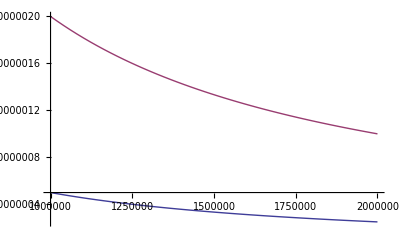

```mathematica
Plot[{-Log[BesselI[1,β]/BesselI[0,β]],-Log[BesselI[2,β]/BesselI[0,β]]},{β,1000000,2000000}]
```

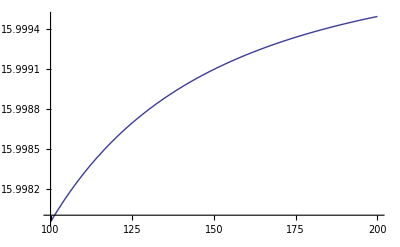

```mathematica
Plot[{Log[BesselI[4,β]/BesselI[0,β]]/Log[BesselI[1,β]/BesselI[0,β]]},{β,100,200}]
```

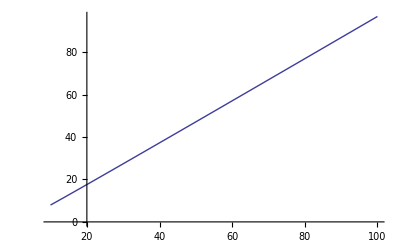

```mathematica
Plot[Log[BesselI[0,β]],{β,10,100}]
```